## Load pre-processing and fitting methods

```mathematica
<< NoTremorProcedures
```

```mathematica
<<NoTremorAnalysis
```

```mathematica
TestType[test_]:= Module[{type,t1,t2},
type=Sign@Max@Abs@Differences[test[[All,3]]];
If[type==1,
t1=Sign@Abs@Differences@test[[All,3]];
t2=Sign@Abs@Differences@test[[All,2]];
If[Total[Abs[t1-t2]]< Min[Total@t1,Total@t2],type=1,type=2]
];type
]
```

#### For iPAD files

```mathematica
ImportTest[filename_]:=Module[{data,begindata,d1,d2,d3,d4,t0,p,pts},
data=Import[filename,"TSV"];
(* begindata=First@First@Position[data,""];*)
begindata=Max@Flatten@Position[Map[Length,data],1];
Print[TableForm@data[[1;;2]]];
data=data[[begindata+1;;-1]];
p=Position[Differences@data[[All,1]],0]; (* remove samples with same time *)
data=Delete[data,p];
p=Position[data[[All,11]],_?(#≠1&)]; (* remove samples without contact *)
data=Delete[data,p];
data=data[[All,{1,8,10,6}]];
Print["Minimum Sample Time (ms) ",Min[Differences@data[[All,1]]]];
Print["Mean Sample Time    (ms) ",N@Mean[Differences@data[[All,1]]]];
Print["Maximum Sample Time (ms) ",Max[Differences@data[[All,1]]]];
(* If[Length@Position[Abs@Differences@data[[All,4]],_?(#>50&)]≠0,Message[jumps::data];Beep[]]; *)

(* remove outliers 2 passes *)
pts=Transpose[{Rest@Differences@data[[All,4]],Differences@Differences@data[[All,4]]}];
p=2+Position[Map[#[[1]]==0.&& #[[2]]≠0.&,pts],True]; (* outliers position *)
data=Delete[data,p];
pts=Transpose[{Rest@Differences@data[[All,4]],Differences@Differences@data[[All,4]]}];
p=2+Position[Map[#[[1]]==0.&& #[[2]]≠0.&,pts],True]; (* outliers position *)
data=Delete[data,p];

(* resample data at 5 ms *)
d1 =Interpolation[data[[All,{1,1}]],InterpolationOrder->1];
d2 =Interpolation[data[[All,{1,2}]],InterpolationOrder->0];
d3 =Interpolation[data[[All,{1,3}]],InterpolationOrder->0];
d4 =Interpolation[data[[All,{1,4}]],InterpolationOrder->1];

t0=d1[First[data[[All,1]]]];

data=Table[{(d1[i]-t0),d2[i],d3[i],0.5 Round[2 d4[i]]},{i,First[data[[All,1]]],Last[data[[All,1]]],0.005}]; (* resampled at 5 ms and keep quantization *)

Print[""];
Print["Data is resampled at 5 ms, here is an excerpt"];
Print[TableForm[N@data[[1;;3,All]],TableHeadings->{{},{"Time (s)","Target","Disturbance","position/force"}}]];
N@data
]
```

```mathematica
QuietImportTest[filename_]:=Module[{data,begindata,d1,d2,d3,d4,t0,p,pts},
data=Import[filename,"TSV"];
(* begindata=First@First@Position[data,""];*)
begindata=Max@Flatten@Position[Map[Length,data],1];
PrintTemporary[TableForm@data[[1;;2]]];
data=data[[begindata+1;;-1]];
p=Position[Differences@data[[All,1]],0]; (* remove samples with same time *)
data=Delete[data,p];
p=Position[data[[All,11]],_?(#≠1&)]; (* remove samples without contact *)
data=Delete[data,p];
data=data[[All,{1,8,10,6}]];

(* remove outliers 2 passes *)
pts=Transpose[{Rest@Differences@data[[All,4]],Differences@Differences@data[[All,4]]}];
p=2+Position[Map[#[[1]]==0.&& #[[2]]≠0.&,pts],True]; (* outliers position *)
data=Delete[data,p];
pts=Transpose[{Rest@Differences@data[[All,4]],Differences@Differences@data[[All,4]]}];
p=2+Position[Map[#[[1]]==0.&& #[[2]]≠0.&,pts],True]; (* outliers position *)
data=Delete[data,p];

(* resample data at 5 ms *)
d1 =Interpolation[data[[All,{1,1}]],InterpolationOrder->1];
d2 =Interpolation[data[[All,{1,2}]],InterpolationOrder->0];
d3 =Interpolation[data[[All,{1,3}]],InterpolationOrder->0];
d4 =Interpolation[data[[All,{1,4}]],InterpolationOrder->1];

t0=d1[First[data[[All,1]]]];

data=Table[{(d1[i]-t0),d2[i],d3[i],d4[i]},{i,First[data[[All,1]]],Last[data[[All,1]]],0.005}]; (* resampled at 5 ms *)

N@data
]
```

#### For PC files

```mathematica
ImportTest[filename_]:=Module[{data,begindata,d1,d2,d3,d4,t0,p,pts},
data=Import[filename,"TSV"];
begindata=First@First@Position[data,""];
Print[TableForm@data[[Min@Position[Map[Length,data],1]]]];
data=data[[begindata+1;;-2]];
p=Position[Differences@data[[All,1]],0];
data=Delete[data,p];
Print["Minimum Sample Time (ms) ",Min[Differences@data[[All,1]]]];
Print["Mean Sample Time    (ms) ",N@Mean[Differences@data[[All,1]]]];
Print["Maximum Sample Time (ms) ",Max[Differences@data[[All,1]]]];
(* If[Length@Position[Abs@Differences@data[[All,4]],_?(#>50&)]≠0,Message[jumps::data];Beep[]]; *)

(* remove outliers 2 passes *)
pts=Transpose[{Rest@Differences@data[[All,4]],Differences@Differences@data[[All,4]]}];
p=2+Position[Map[#[[1]]==0.&& #[[2]]≠0.&,pts],True]; (* outliers position *)
data=Delete[data,p];
pts=Transpose[{Rest@Differences@data[[All,4]],Differences@Differences@data[[All,4]]}];
p=2+Position[Map[#[[1]]==0.&& #[[2]]≠0.&,pts],True]; (* outliers position *)
data=Delete[data,p];

(* resample data at 5 ms *)
d1 =Interpolation[data[[All,{1,1}]],InterpolationOrder->1];
d2 =Interpolation[data[[All,{1,2}]],InterpolationOrder->0];
d3 =Interpolation[data[[All,{1,3}]],InterpolationOrder->0];
d4 =Interpolation[data[[All,{1,4}]],InterpolationOrder->1];

t0=d1[First[data[[All,1]]]];

data=Table[{0.001 (d1[i]-t0),d2[i],d3[i],d4[i]},{i,First[data[[All,1]]],Last[data[[All,1]]],5}]; (* resampled at 5 ms *)

Print[""];
Print["Data is resampled at 5 ms, here is an excerpt"];
Print[TableForm[N@data[[1;;3,All]],TableHeadings->{{},{"Time (s)","Target","Disturbance","position/force"}}]];
N@data
]
```

```mathematica
QuietImportTest[filename_]:=Module[{data,begindata,d1,d2,d3,d4,t0,p,pts},
data=Import[filename,"TSV"];
begindata=First@First@Position[data,""];
PrintTemporary[StringTake[First@data[[Min@Position[Map[Length,data],1]]],-18]];
data=data[[begindata+1;;-2]];
p=Position[Differences@data[[All,1]],0];
data=Delete[data,p];
(* Print["  Min/Max Sample Time (ms) ",Min[Differences@data[[All,1]]]," ",Max[Differences@data[[All,1]]]];*)
(* If[Length@Position[Abs@Differences@data[[All,4]],_?(#>50&)]≠0,Message[jumps::data];Beep[]];*)

(* remove outliers 2 passes *)
pts=Transpose[{Rest@Differences@data[[All,4]],Differences@Differences@data[[All,4]]}];
p=2+Position[Map[#[[1]]==0.&& #[[2]]≠0.&,pts],True]; (* outliers position *)
data=Delete[data,p];
pts=Transpose[{Rest@Differences@data[[All,4]],Differences@Differences@data[[All,4]]}];
p=2+Position[Map[#[[1]]==0.&& #[[2]]≠0.&,pts],True]; (* outliers position *)
data=Delete[data,p];

(* resample data at 5 ms *)
d1 =Interpolation[data[[All,{1,1}]],InterpolationOrder->1];
d2 =Interpolation[data[[All,{1,2}]],InterpolationOrder->0];
d3 =Interpolation[data[[All,{1,3}]],InterpolationOrder->0];
d4 =Interpolation[data[[All,{1,4}]],InterpolationOrder->1];

t0=d1[First[data[[All,1]]]];

data=Table[{0.001 (d1[i]-t0),d2[i],d3[i],d4[i]},{i,First[data[[All,1]]],Last[data[[All,1]]],5}]; (* resampled at 5 ms *)

N@data
]
```

#### Other porcedures

```mathematica
ProcessUserRaw[cohort_,user_,OnOff_,LineForce_]:= Module[{mode,win=2.6,UserAll,plain,distractor,UserAll2,p1,p2},
mode=(* "/"<>user<>"_"<>OnOff<> "/"<>LineForce<>no subdirectories all in ON state ?*)"/";
UserAll=ImportUser[cohort<>user<>mode];p1="";p2="";
If[Length@UserAll>0,
If[LineForce=="line",
plain=Flatten@Position[Map[TestType[#]&,UserAll],0];
p1=Table[PlotValidEvents[UserAll[[i]],win,_?(#>180&)],{i,plain}];
distractor=Flatten@Position[Map[TestType[#]&,UserAll],1];
p2=Table[PlotValidEvents[UserAll[[i]],win,_?(#>180&)],{i,distractor}];
,
plain=Flatten@Position[Map[TestType[#]&,UserAll],0];
p1=Table[PlotTest[UserAll[[i]]],{i,plain}];
distractor=Flatten@Position[Map[TestType[#]&,UserAll],1];
p2=Table[PlotTest[UserAll[[i]]],{i,distractor}];
]
];
Flatten@{user<>" "<>OnOff<>" "<>LineForce,p1,p2}
]
```

```mathematica
ProcessUser[cohort_,user_,OnOff_,LineForce_]:= Module[{mode,win=2.6,UserAll,plain,distractor,delays1,delays2,p1,p2,p3,p4,p5,p6,mt901,mt902,mv1,mv2,frms},
mode= (* "/"<>user<>"_"<>OnOff<> *) "/"<>LineForce<>"/";
UserAll=ImportUser[cohort<>user<>mode];p1="";p2="";p3="";p4="";
If[Length@UserAll>0,
If[LineForce=="line",
plain=Flatten@Position[Map[TestType[#]&,UserAll],0];
distractor=Flatten@Position[Map[TestType[#]&,UserAll],1];
delays1=0.005 Delays[Flatten[UserAll[[plain]],1],win,_?(#>180&)];
delays2=0.005 Delays[Flatten[UserAll[[distractor]],1],win,_?(#>180&)];
p1=PlotExtractEvents[Flatten[UserAll[[plain]],1],win,_?(#>180&)];
mt901 =0.005 Map[Max@Position[Threshold[#,0.9],0.]&,ExtractEvents[Flatten[UserAll[[plain]],1],win,_?(#>180&)]];
p2=PlotExtractEvents[Flatten[UserAll[[distractor]],1],win,_?(#>180&)];
mt902 =0.005 Map[Max@Position[Threshold[#,0.9],0.]&,ExtractEvents[Flatten[UserAll[[distractor]],1],win,_?(#>180&)]];
p3=PlotMeanSpeedEvent[Flatten[UserAll[[plain]],1],win,_?(#>180&)];
mv1=Max@GaussianFilter[Differences@Mean@AlignEvents[Flatten[UserAll[[plain]],1],win,_?(#>180&)],5.]/0.005;
p4=PlotMeanSpeedEvent[Flatten[UserAll[[distractor]],1],win,_?(#>180&)];
mv2=Max@GaussianFilter[Differences@Mean@AlignEvents[Flatten[UserAll[[distractor]],1],win,_?(#>180&)],5.]/0.005;
p5=PlotMeanEvent[Flatten[UserAll[[plain]],1],win,_?(#>180&)];
p6=PlotMeanEvent[Flatten[UserAll[[distractor]],1],win,_?(#>180&)];

Flatten@{user<>" "<>OnOff<>" "<>LineForce,
N@Mean@delays1,N@StandardDeviation@delays1,N@Mean@(mt901-delays1),N@StandardDeviation@(mt901-delays1),mv1,p1,p3,p5,
N@Mean@delays2,N@StandardDeviation@delays2,N@Mean@(mt902-delays2),N@StandardDeviation@(mt902-delays2),mv2, p2,p4,p6}
,
plain=Flatten@Position[Map[TestType[#]&,UserAll],0];
distractor=Flatten@Position[Map[TestType[#]&,UserAll],1];
frms=Map[RootMeanSquare,UserAll[[All,4000;;-1,4]]-UserAll[[All,4000;;-1,2]]];
{Mean[frms[[plain]]],Mean[frms[[distractor]]]}
]
]
]
```

### Define PlotValidEvents, to plot the distractor line if present

```mathematica
ValidEvents[data_,timewindow_,criterion_]:=Module[{t,u,d,y,window,start,samples,valid,steps,clusters,i},
{t,u,d,y}=Transpose@data;
window=IntegerPart[timewindow/.005];
start=SelectStepsEvents[data,timewindow,criterion];
samples=Table[y[[i;;i+window]],{i,start}];
samples=Map[Accumulate[Differences[#]]&,samples];
valid=Flatten@Position[Map[Max,Abs@samples[[All,1;;40]]],_?(#≤1.&)]; (* ignore samples with movement in the first 0.2s *)
valid=Intersection[valid,Flatten[Position[Map[Max@Abs@Differences[#]&,samples],_?(#<31&)]]]; (* detect jumps *)
start=start[[valid]];
samples=Table[y[[i;;i+window]],{i,start}]; (* remove outliers *)
samples=Map[Accumulate[Differences[#]]&,samples];
steps=Table[u[[i+1]]-u[[i]],{i,start}];
samples=Table[samples[[i]]/steps[[i]],{i,Length@start}]; (* find normalised smaples *)
clusters=FindClusters[Map[Last,samples]->Range[Length@samples],Method->"Agglomerate"]; (* clusterize outliers *) 
samples=samples[[Flatten@Select[clusters,Length@#>1&]]] ;(* ignore outliers *)
start=start[[Flatten@Select[clusters,Length@#>1&]]] ;(* ignore outliers *)
clusters=FindClusters[Map[Last,samples]->Range[Length@samples],Method->"Agglomerate"]; (* clusterize outliers *) 
start[[Flatten@Select[clusters,Length@#>1&]]] (* ignore outliers *)
]
```

```mathematica
PlotValidEvents[data_,timewindow_,criterion_]:=Module[{t,u,d,y,start,window,events,top},
{t,u,d,y}=Transpose@data;
top=If[Max[u]>1000,1920,1024];
window=IntegerPart[timewindow/.005];
start=ValidEvents[data,timewindow,criterion];
events=Table[0,{Length[u]}]; 
events=ReplacePart[events,Table[i->1920,{i,start}]];
events=ReplacePart[events,Table[i+window->-1920,{i,start}]];
events=Accumulate[events];
ListPlot[{Transpose[{t,y}],Transpose[{t,u}],Transpose[{t,events}],Transpose[{t,d}]},Joined->{False,True,True,True},Filling->{3->0},PlotStyle->{Opacity[0.9],{Cyan,Opacity[0.4]},None,{Red,Opacity[0.4]}},
AspectRatio->0.3,ImageSize->900,Frame->True,PlotRange->{{0,Last@t},{0,top}},
FrameLabel->{"Time (s)","Displacement  (pixels)"},LabelStyle->Directive[FontSize->14],FrameStyle->Directive[Thickness[0.0005]],FrameTicks->{{Automatic,None},{Automatic,None}}]
];
```

```mathematica
Delays[data_,timewindow_,criterion_]:=Module[{t,u,d,y,start,window,events,samples,steps,delays},
{t,u,d,y}=Transpose@data;
window=IntegerPart[timewindow/.005];
start=ValidEvents[data,timewindow,criterion];
samples=Table[y[[i;;i+window]],{i,start}];
samples=Map[Accumulate[Differences[#]]&,samples];
steps=Table[u[[i+1]]-u[[i]],{i,start}];
samples=Table[Threshold[samples[[i]]Sign[steps[[i]]],10.],{i,Length@start}];
delays=Table[Max@Position[samples[[i]],0.],{i,Length@start}]
]
```

```mathematica
DelayCycles[data_,timewindow_,criterion_]:=Module[{r=8,t,u,d,y,start,window,events,samples,steps,sides,len,i,k,m},
{t,u,d,y}=Transpose@data;
window=IntegerPart[timewindow/.005];
start=ValidEvents[data,timewindow,criterion];
samples=Table[y[[i;;i+window]],{i,start}];
samples=Map[Sign[Differences[#]]&,samples];
steps=Table[u[[i+1]]-u[[i]],{i,start}];
samples=Table[samples[[i]]*Sign@steps[[i]],{i,Length@start}];
samples=Map[ArrayPad[MedianFilter[ArrayPad[#,r],r],-r]&,samples]; (* remove events shorter tha r *)
m=Map[Position[#,1]-1&,samples]/.{}->{{0}};m=m[[All,1,1]];
k=Map[Position[#,-1]-1&,samples]/.{}->{{0}};k=k[[All,1,1]];
Table[If[Abs@k[[i]]>0,If[Abs@m[[i]]< Abs@k[[i]],m[[i]],-k[[i]]],m[[i]]],{i,1,Length@m}]
]
```

### import raw raw

```mathematica
ImportTestRaw[filename_]:=Module[{data,begindata,d1,d2,d3,d4,t0,p,pts},
data=Import[filename,"TSV"];
(* begindata=First@First@Position[data,""];*)
begindata=Max@Flatten@Position[Map[Length,data],1];
Print[TableForm@data[[1;;2]]];
data=data[[begindata+1;;-1]];
p=Position[Differences@data[[All,1]],0]; (* remove samples with same time *)
data=Delete[data,p];
p=Position[data[[All,11]],_?(#≠1&)]; (* remove samples without contact *)
data=Delete[data,p];
data=data[[All,{1,8,10,6}]] . {{1000,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,0}} ;
Print["Minimum Sample Time (ms) ", Min[Differences@data[[All,1]]]];
Print["Mean Sample Time    (ms) ", N@Mean[Differences@data[[All,1]]]];
Print["Maximum Sample Time (ms) ", Max[Differences@data[[All,1]]]];

N@data
]
```

```mathematica
AlignRawEvents[data_,timewindow_,criterion_]:=Module[{t,u,d,y,start,window,events,samples,steps,delays},
{t,u,d,y}=Transpose@data;
window=IntegerPart[timewindow/.005];
start=ValidEvents[data,timewindow,criterion];
samples=Table[y[[i;;i+window]],{i,start}];
samples=Map[Accumulate[Differences[#]]&,samples];
steps=Table[Sign[u[[i+1]]-u[[i]]],{i,start}];
samples=Table[Threshold[samples[[i]]Sign[steps[[i]]],10.],{i,Length@start}];
delays=Table[Max@Position[samples[[i]],0.],{i,Length@start}];
start=start+delays-Round@Median@delays;
samples=Table[y[[i;;i+window]],{i,start}];
samples=Map[Accumulate[Differences[#]]&,samples];
samples=Table[samples[[i]]/steps[[i]],{i,Length@start}]
]
```

```mathematica
PlotAlignRawEvents[data_,timewindow_,criterion_]:= Module[{samples},
samples=AlignRawEvents[data,timewindow,criterion];
samples =FindClusters[samples,5];
samples =Map[Differences[Mean[#]]/0.005&,samples] 0.0254/132;
samples= Table[Transpose[{0.005 Range[Length@samples[[i]]],samples[[i]]}],{i,1,Length@samples}];
Show[ListPlot[samples,Joined->{True},ImageSize->400,Frame->True,PlotRange->{Automatic,{-0.05,0.4}},PlotStyle->{Opacity[0.8]},
FrameLabel->{"Time (s)","Speed (m/s)"},LabelStyle->Directive[FontSize->14],FrameStyle->Directive[Thickness[0.0005]],FrameTicks->{{0.1 Range[0,10],None},{Automatic,None}}],
Graphics[{Thin,Gray,Line[{{0.,0.},{5.,0.}}]}]
]
]
```

```mathematica
ExtractRawEvents[data_,timewindow_,criterion_]:=Module[{t,u,d,y,start,window,events,samples,steps},
{t,u,d,y}=Transpose@data;
window=IntegerPart[timewindow/.005];
start=ValidEvents[data,timewindow,criterion];
samples=Table[y[[i;;i+window]],{i,start}];
samples=Map[Accumulate[Differences[#]]&,samples];
steps=Table[u[[i+1]]-u[[i]],{i,start}];
samples=Table[samples[[i]]/Sign@steps[[i]],{i,Length@start}]
]
```

```mathematica
PlotTimelineEvents[data_,timewindow_,criterion_]:= Module[{samples,delays},
samples=ExtractRawEvents[data,timewindow,criterion];
samples= Table[Transpose[{0.005 Range[Length@samples[[i]]-1],i+0.4Sign@Differences@samples[[i]]}],{i,1,Length@samples}];
delays=DelayCycles[data,timewindow,criterion];
delays=Table[{0.005 Abs@delays[[i]],i+0.4 Sign@delays[[i]]},{i,1,Length@delays}];
Show[
ListPlot[samples,Joined->{True},ImageSize->400,Frame->True,PlotRange->{Automatic,Automatic},PlotStyle->{Opacity[0.8]},Filling->{Table[i->i,{i,1,Length@samples}]},
FrameLabel->{"Time (s)","Direction of movement"},LabelStyle->Directive[FontSize->14],FrameStyle->Directive[Thickness[0.0005]],FrameTicks->{{Automatic,None},{Automatic,None}},AspectRatio->GoldenRatio],
ListPlot[delays, PlotStyle->Red]]
]
```

```mathematica
PlotMeanTimelineEvent[data_,timewindow_,criterion_]:= Module[{samples,s1,s2},
samples=Table[Map[Sign[Differences[#]]&,ExtractRawEvents[d,timewindow,criterion]],{d,data}];
samples=Flatten[samples,{{1,2},{3}}];
s1=Mean[N[samples]/.-1.->0.];
s2=Mean[N[samples]/. 1.->0.];
samples={ Transpose[{0.005 Range[Length@s1],s1}],Transpose[{0.005 Range[Length@s2],s2}]};
ListPlot[samples,Joined->{True},ImageSize->400,Frame->True,PlotRange->{Automatic,All},PlotStyle->{Opacity[0.8]},Filling->{1->0,2->0},
FrameLabel->{"Time (s)","Probability of movement"},LabelStyle->Directive[FontSize->14],FrameStyle->Directive[Thickness[0.0005]],FrameTicks->{{Automatic,None},{Automatic,None}}]
]
```

## Automatic processing of all users raw data

```mathematica
shef=NotebookDirectory[];SetDirectory[shef]
```

/Users/mauro/Dropbox (Personale)/linetask/2014_shef_expt/analysis/AllData

### Import and process user

```mathematica
files=Flatten@Map[StringSplit[#,"'"][[All,-2]]&,Import["allfiles.m","TSV"]]
```

{Jon/EF/line/20141118134208.txt,Jon/EF/line/20141118133619.txt,Jon/EF/line/20141118133914.txt,Jon/SF/line/20141125145758.txt,Jon/SF/line/20141125145535.txt,Jon/SF/line/20141125145313.txt,Jon/EJ/line/20141201164116.txt,Jon/EJ/line/20141201164343.txt,Jon/EJ/line/20141201164607.txt,Jon/EC2/line/20141118132305.txt,Jon/EC2/line/20141118132030.txt,Jon/EC2/line/20141118131733.txt,Jon/EW2_/line/20141202162631.txt,Jon/EW2_/line/20141202162900.txt,Jon/EW2_/line/20141202163117.txt,Jon/AW3_/line/20141125144037.txt,Jon/AW3_/line/20141125143811.txt,Jon/AW3_/line/20141125143541.txt,Jon/AB1_/line/20141202151037.txt,Jon/AB1_/line/20141202150810.txt,Jon/AB1_/line/20141202151303.txt,Jon/EM2/line/20141125142451.txt,Jon/EM2/line/20141125141940.txt,Jon/EM2/line/20141125142218.txt,Jon/SY/line/20141125153747.txt,Jon/SY/line/20141125154012.txt,Jon/SY/line/20141125153525.txt,Jon/SS/line/20141202153901.txt,Jon/SS/line/20141202154138.txt,Jon/SS/line/20141202154416.txt,Katie/JS/line/20141117163927.txt,Katie/JS/line/20141117163702.txt,Katie/JS/line/20141117163429.txt,Katie/LK_/line/20141117141428.txt,Katie/LK_/line/20141117141945.txt,Katie/LK_/line/20141117141712.txt,Katie/KC/line/20141124135111.txt,Katie/KC/line/20141124135601.txt,Katie/KC/line/20141124135341.txt,Katie/CP/line/20141117165409.txt,Katie/CP/line/20141117165937.txt,Katie/CP/line/20141117165702.txt,Katie/RF/line/20141201142950.txt,Katie/RF/line/20141201143224.txt,Katie/RF/line/20141201142720.txt,Katie/GM/line/20141201141617.txt,Katie/GM/line/20141201142107.txt,Katie/GM/line/20141201141843.txt,Katie/JT2/line/20141201135316.txt,Katie/JT2/line/20141201135547.txt,Katie/JT2/line/20141201135816.txt,Katie/RC/line/20141124133740.txt,Katie/RC/line/20141124133516.txt,Katie/RC/line/20141124134019.txt,Katie/AW2_/line/20141201133936.txt,Katie/AW2_/line/20141201134221.txt,Katie/AW2_/line/20141201133652.txt,Katie/JF/line/20141124131114.txt,Katie/JF/line/20141124130847.txt,Katie/JF/line/20141124131349.txt,Katie/EK/line/20141117161119.txt,Katie/EK/line/20141117161422.txt,Katie/EK/line/20141117161656.txt,Katie/TC/line/20141117160429.txt,Katie/TC/line/20141117160208.txt,Katie/TC/line/20141117155942.txt,Rachel/IR/line/20141118135611.txt,Rachel/IR/line/20141118140131.txt,Rachel/IR/line/20141118135857.txt,Rachel/HY/line/20141118150740.txt,Rachel/HY/line/20141118150509.txt,Rachel/HY/line/20141118151002.txt,Rachel/EB2/line/20141118165737.txt,Rachel/EB2/line/20141118170002.txt,Rachel/EB2/line/20141118170220.txt,Rachel/AW1_/line/20141118163209.txt,Rachel/AW1_/line/20141118163657.txt,Rachel/AW1_/line/20141118163434.txt,Rachel/AL_/line/20141118143431.txt,Rachel/AL_/line/20141118143714.txt,Rachel/AL_/line/20141118143142.txt,Rachel/RQ/line/20141201153403.txt,Rachel/RQ/line/20141201153635.txt,Rachel/RQ/line/20141201153857.txt,Rachel/CD2/line/20141201161633.txt,Rachel/CD2/line/20141201161856.txt,Rachel/CD2/line/20141201161412.txt,Rachel/IB/line/20141118142211.txt,Rachel/IB/line/20141118141933.txt,Rachel/IB/line/20141118141658.txt,Rachel/PO/line/20141127164137.txt,Rachel/PO/line/20141127163907.txt,Rachel/PO/line/20141127164406.txt,Rachel/CM/line/20141201145821.txt,Rachel/CM/line/20141201150052.txt,Rachel/CM/line/20141201150322.txt,Rachel/GB/line/20141118153932.txt,Rachel/GB/line/20141118153448.txt,Rachel/GB/line/20141118153713.txt,Rachel/PB/line/20141118152100.txt,Rachel/PB/line/20141118152557.txt,Rachel/PB/line/20141118152327.txt,Olivia/BG/line/20141120153210.txt,Olivia/BG/line/20141120153432.txt,Olivia/BG/line/20141120152941.txt,Olivia/MC/line/20141120140859.txt,Olivia/MC/line/20141120140639.txt,Olivia/MC/line/20141120140412.txt,Olivia/SB2/line/20141204150147.txt,Olivia/SB2/line/20141204145711.txt,Olivia/SB2/line/20141204145931.txt,Olivia/EC1/line/20141120150825.txt,Olivia/EC1/line/20141120150603.txt,Olivia/EC1/line/20141120151051.txt,Olivia/AS/line/20141120151830.txt,Olivia/AS/line/20141120151543.txt,Olivia/AS/line/20141120152053.txt,Olivia/CD1/line/20141120141526.txt,Olivia/CD1/line/20141120142010.txt,Olivia/CD1/line/20141120141751.txt,Olivia/LS/line/20141120145546.txt,Olivia/LS/line/20141120150043.txt,Olivia/LS/line/20141120145821.txt,Olivia/TM/line/20141127153903.txt,Olivia/TM/line/20141127154340.txt,Olivia/TM/line/20141127154121.txt,Olivia/RG/line/20141204142043.txt,Olivia/RG/line/20141204142320.txt,Olivia/RG/line/20141204142538.txt,Olivia/LH2/line/20141120160008.txt,Olivia/LH2/line/20141120155742.txt,Olivia/LH2/line/20141120160232.txt,Aizat/NA/line/20141204143400.txt,Aizat/NA/line/20141204143127.txt,Aizat/NA/line/20141204143624.txt,Aizat/AM/line/20141127162309.txt,Aizat/AM/line/20141127162049.txt,Aizat/AM/line/20141127161812.txt,Aizat/EW1_/line/20141127133729.txt,Aizat/EW1_/line/20141127133217.txt,Aizat/EW1_/line/20141127133502.txt,Aizat/RD/line/20141204155500.txt,Aizat/RD/line/20141204155722.txt,Aizat/RD/line/20141204155938.txt,Aizat/CH/line/20141127140100.txt,Aizat/CH/line/20141127140328.txt,Aizat/CH/line/20141127135828.txt,Aizat/KR/line/20141204131542.txt,Aizat/KR/line/20141204131811.txt,Aizat/KR/line/20141204132035.txt,Aizat/NC/line/20141204135451.txt,Aizat/NC/line/20141204135216.txt,Aizat/NC/line/20141204135718.txt,Aizat/LH1/line/20141127143241.txt,Aizat/LH1/line/20141127143811.txt,Aizat/LH1/line/20141127143527.txt,Aizat/EB1/line/20141204161129.txt,Aizat/EB1/line/20141204160911.txt,Aizat/EB1/line/20141204160639.txt,Aizat/SB1/line/20141127152533.txt,Aizat/SB1/line/20141127152305.txt,Aizat/SB1/line/20141127152028.txt,Aizat/JT1/line/20141127142244.txt,Aizat/JT1/line/20141127141708.txt,Aizat/JT1/line/20141127142007.txt}

```mathematica
dates=Map[DateObject@ToExpression[#]&,Map[{StringTake[#,{-18,-15}],StringTake[#,{-14,-13}],StringTake[#,{-12,-11}],StringTake[#,{-10,-9}],StringTake[#,{-8,-7}],StringTake[#,{-6,-5}]}&,files]];
```

```mathematica
all=Table[QuietImportTest[filename],{filename,files}];
```

```mathematica
subjects=MapThread[Append,{Map[StringSplit[#,"/"][[1;;2]]&,files],Map[TestType,all]}]
```

{{Jon,EF,1},{Jon,EF,0},{Jon,EF,2},{Jon,SF,0},{Jon,SF,1},{Jon,SF,2},{Jon,EJ,2},{Jon,EJ,0},{Jon,EJ,1},{Jon,EC2,2},{Jon,EC2,1},{Jon,EC2,0},{Jon,EW2_,1},{Jon,EW2_,2},{Jon,EW2_,0},{Jon,AW3_,0},{Jon,AW3_,2},{Jon,AW3_,1},{Jon,AB1_,1},{Jon,AB1_,0},{Jon,AB1_,2},{Jon,EM2,2},{Jon,EM2,0},{Jon,EM2,1},{Jon,SY,0},{Jon,SY,2},{Jon,SY,1},{Jon,SS,2},{Jon,SS,1},{Jon,SS,0},{Katie,JS,1},{Katie,JS,2},{Katie,JS,0},{Katie,LK_,0},{Katie,LK_,2},{Katie,LK_,1},{Katie,KC,2},{Katie,KC,1},{Katie,KC,0},{Katie,CP,1},{Katie,CP,0},{Katie,CP,2},{Katie,RF,0},{Katie,RF,1},{Katie,RF,2},{Katie,GM,1},{Katie,GM,0},{Katie,GM,2},{Katie,JT2,1},{Katie,JT2,0},{Katie,JT2,2},{Katie,RC,1},{Katie,RC,0},{Katie,RC,2},{Katie,AW2_,2},{Katie,AW2_,1},{Katie,AW2_,0},{Katie,JF,0},{Katie,JF,1},{Katie,JF,2},{Katie,EK,2},{Katie,EK,0},{Katie,EK,1},{Katie,TC,2},{Katie,TC,0},{Katie,TC,1},{Rachel,IR,0},{Rachel,IR,2},{Rachel,IR,1},{Rachel,HY,1},{Rachel,HY,2},{Rachel,HY,0},{Rachel,EB2,1},{Rachel,EB2,0},{Rachel,EB2,2},{Rachel,AW1_,2},{Rachel,AW1_,1},{Rachel,AW1_,0},{Rachel,AL_,0},{Rachel,AL_,1},{Rachel,AL_,2},{Rachel,RQ,0},{Rachel,RQ,2},{Rachel,RQ,1},{Rachel,CD2,0},{Rachel,CD2,2},{Rachel,CD2,1},{Rachel,IB,2},{Rachel,IB,0},{Rachel,IB,1},{Rachel,PO,1},{Rachel,PO,0},{Rachel,PO,2},{Rachel,CM,0},{Rachel,CM,1},{Rachel,CM,2},{Rachel,GB,2},{Rachel,GB,0},{Rachel,GB,1},{Rachel,PB,1},{Rachel,PB,0},{Rachel,PB,2},{Olivia,BG,2},{Olivia,BG,1},{Olivia,BG,0},{Olivia,MC,2},{Olivia,MC,0},{Olivia,MC,1},{Olivia,SB2,2},{Olivia,SB2,1},{Olivia,SB2,0},{Olivia,EC1,1},{Olivia,EC1,0},{Olivia,EC1,2},{Olivia,AS,1},{Olivia,AS,2},{Olivia,AS,0},{Olivia,CD1,1},{Olivia,CD1,0},{Olivia,CD1,2},{Olivia,LS,2},{Olivia,LS,1},{Olivia,LS,0},{Olivia,TM,1},{Olivia,TM,0},{Olivia,TM,2},{Olivia,RG,0},{Olivia,RG,1},{Olivia,RG,2},{Olivia,LH2,0},{Olivia,LH2,1},{Olivia,LH2,2},{Aizat,NA,2},{Aizat,NA,0},{Aizat,NA,1},{Aizat,AM,0},{Aizat,AM,1},{Aizat,AM,2},{Aizat,EW1_,2},{Aizat,EW1_,0},{Aizat,EW1_,1},{Aizat,RD,1},{Aizat,RD,2},{Aizat,RD,0},{Aizat,CH,0},{Aizat,CH,2},{Aizat,CH,1},{Aizat,KR,0},{Aizat,KR,1},{Aizat,KR,2},{Aizat,NC,1},{Aizat,NC,2},{Aizat,NC,0},{Aizat,LH1,0},{Aizat,LH1,1},{Aizat,LH1,2},{Aizat,EB1,1},{Aizat,EB1,0},{Aizat,EB1,2},{Aizat,SB1,2},{Aizat,SB1,0},{Aizat,SB1,1},{Aizat,JT1,1},{Aizat,JT1,2},{Aizat,JT1,0}}

```mathematica
delays=Table[0.005 DelayCycles[i,1.0,_?(#>100&)],{i,all}];
```

```mathematica
Metrics[z_]:=Module[{d1,d2},
d1=Select[z,#>0.&];
d2=Select[z,#<0.&];
{Mean@d1,StandardDeviation@d1,Length@d1,If[Length@d2>0,-Mean@d2],If[Length@d2>1,StandardDeviation@d2],Length@d2, N@Length@d2/Length@d1}
]
```

```mathematica
summary=Map[Quiet@Metrics[#]&,delays]/.Null->"";
```

```mathematica
headers={"Experimenter","Subject","Distractor type","RT (M)", "RT (SD)","N correct","RT incorrect (M)", "RT incorrect (SD)","N incorrect","Error rate","Delays (negative = incorrect)" }
```

{Experimenter,Subject,Distractor type,RT (M),RT (SD),N correct,RT incorrect (M),RT incorrect (SD),N incorrect,Error rate,Delays (negative = incorrect)}

```mathematica
data=Table[Join[subjects[[i]],summary[[i]],delays[[i]]],{i,1,Length@delays}];
```

```mathematica
Export[NotebookDirectory[]<>"Summary.xls",Prepend[data,headers]]
```

/Users/mauro/Dropbox (Personale)/linetask/2014_shef_expt/analysis/AllData/Summary.xls

#### make weekly gropus

```mathematica
plain=Flatten@Position[Map[TestType,all],0]
```

{1,5,8,10,15,16,19,22,26,29,33,36,37,41,44,47,51,53,55,60,61,65,68,70,74,76,81,84,86,88,92,95,97,101,105,108,109,112,116,120,122,124,127,131,134,136,141,144,145,150,151,154,158,162,164}

```mathematica
distractor=Flatten@Position[Map[TestType,all],1]
```

{2,4,9,12,13,17,21,23,25,30,32,34,38,42,43,46,49,54,56,59,63,64,67,71,75,77,79,83,85,89,91,96,99,100,103,107,110,114,115,118,123,125,129,130,135,137,140,142,146,149,152,156,157,160,165}

```mathematica
asyncdistractor=Flatten@Position[Map[TestType,all],2]
```

{3,6,7,11,14,18,20,24,27,28,31,35,39,40,45,48,50,52,57,58,62,66,69,72,73,78,80,82,87,90,93,94,98,102,104,106,111,113,117,119,121,126,128,132,133,138,139,143,147,148,153,155,159,161,163}

#### Inspect data (if necessary)

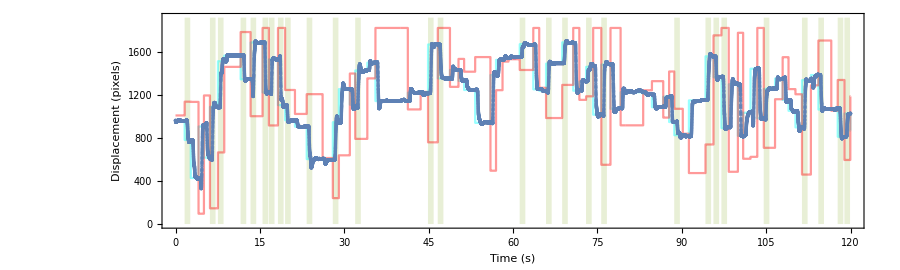

```mathematica
p1=PlotValidEvents[all[[First@distractor]],1.0,_?(#>100&)]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_event_sample.tif",Rasterize[p1,"Image",RasterSize->3000],"ImageEncoding"->"ZIP"];
```

```mathematica
Manipulate[PlotExtractEvents[all[[i]],1.5,_?(#>100&)],{i,1,Length@all,1}];
```

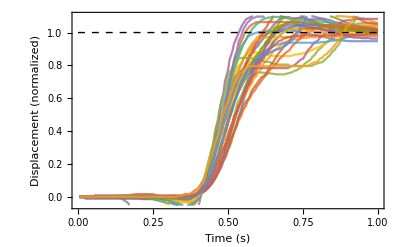

```mathematica
p1=PlotAlignEvents[all[[First@distractor]],1.0,_?(#>100&)]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_aling_event_sample.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

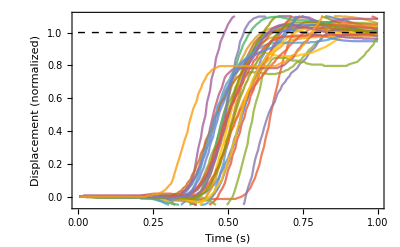

```mathematica
p1=PlotExtractEvents[all[[First@distractor]],1.0,_?(#>100&)]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_extract_event_sample.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

N samples  15 0.454768

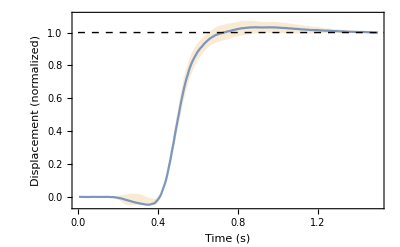

```mathematica
p1 = PlotMeanEvent[all[[First@distractor]],1.5,_?(#>100&)]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_mean_event_sample.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

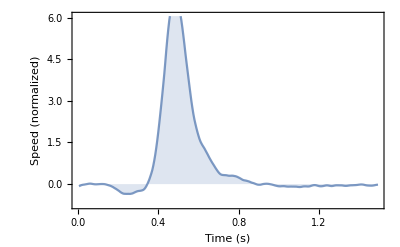

```mathematica
p1 = PlotMeanSpeedEvent[all[[First@distractor]],1.5,_?(#>100&)]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_meanspeed_event_sample.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

#### Delays and movement patterns

```mathematica
Delays[all[[1]],1.0,_?(#>100&)]
```

{66,94,77,76,64,68,60,56,71,65,68,72,65,75,64,57,60,59,67,61,63,64,67,67,66,63,61,58,75}

```mathematica
DelayCycles[all[[1]],1.0,_?(#>100&)]
```

{57,85,71,67,55,58,49,47,60,57,54,65,53,63,54,46,52,49,53,53,54,53,57,56,53,57,52,48,65}

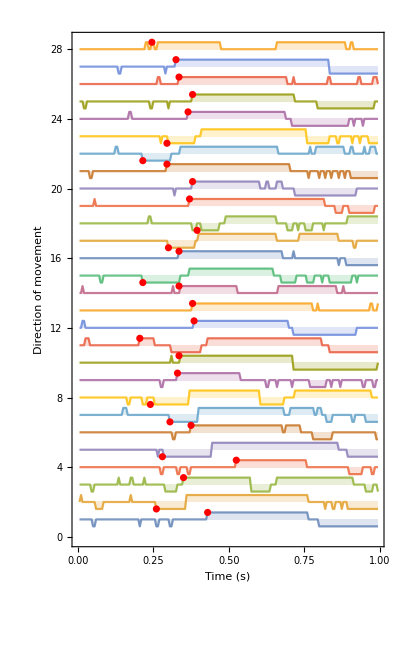

```mathematica
p1=PlotTimelineEvents[all[[First@distractor]],1.0,_?(#>100&)]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_pattern_distractor.tif",Rasterize[p1,"Image",RasterSize->3000],"ImageEncoding"->"ZIP"];
```

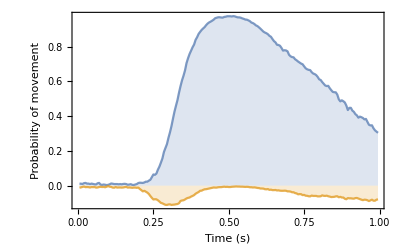

```mathematica
p1=PlotMeanTimelineEvent[all[[distractor]],1.0,_?(#>100&)]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_movement_probability_distractor.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

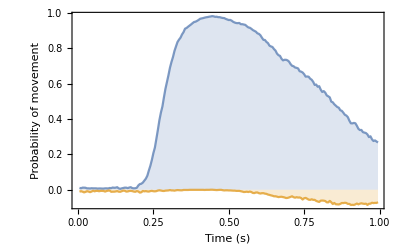

```mathematica
p1=PlotMeanTimelineEvent[all[[plain]],1.0,_?(#>100&)]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_movement_probability_plain.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

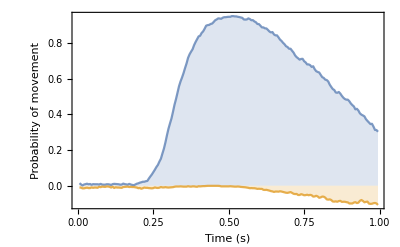

```mathematica
p1=PlotMeanTimelineEvent[all[[asyncdistractor]],1.0,_?(#>100&)]
```

#### Error rates plain

```mathematica
z=Flatten@Table[0.005 DelayCycles[i,1.0,_?(#>100&)],{i,all[[plain]]}];errorrate=N@Count[z,_?(#<0&)]/Length@z
```

0.00520833

```mathematica
Mean@Select[z,#>0.&]
```

0.292624

```mathematica
StandardDeviation@Select[z,#>0.&]
```

0.0528536

```mathematica
Mean@Select[z,#<0.&]
```

-0.245625

```mathematica
StandardDeviation@Select[z,#<0.&]
```

0.0480652

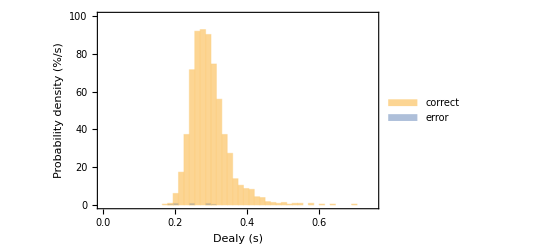

```mathematica
p1=Histogram[{Select[z,#>0.&],-Select[z,#<0.&]},{0.015},100 #2/Length@z/0.15&,PlotRange->{{0,0.75},{0,100}},Frame->True,FrameLabel->{"Dealy (s)","Probability density (%/s)"},LabelStyle->Directive[FontSize->14],FrameStyle->Directive[Thickness[0.0005]],ChartLegends->{"correct","error"}]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>"_rt_plain.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

#### Error rates distractor

```mathematica
z=Flatten@Table[0.005 DelayCycles[i,1.0,_?(#>100&)],{i,all[[distractor]]}];errorrate=N@Count[z,_?(#<0&)]/Length@z
```

0.134603

```mathematica
Mean@Select[z,#>0.&]
```

0.329932

```mathematica
StandardDeviation@Select[z,#>0.&]
```

0.0555331

```mathematica
Mean@Select[z,#<0.&]
```

-0.27722

```mathematica
StandardDeviation@Select[z,#<0.&]
```

0.0570502

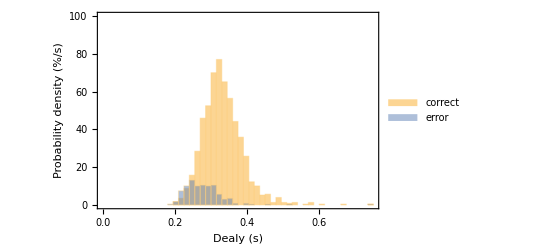

```mathematica
p1=Histogram[{Select[z,#>0.&],-Select[z,#<0.&]},{0.015},100 #2/Length@z/0.15&,PlotRange->{{0,0.75},{0,100}},Frame->True,FrameLabel->{"Dealy (s)","Probability density (%/s)"},LabelStyle->Directive[FontSize->14],FrameStyle->Directive[Thickness[0.0005]],ChartLegends->{"correct","error"}]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>"_rt_distractor.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

#### Error rates async distractor

```mathematica
z=Flatten@Table[0.005 DelayCycles[i,1.0,_?(#>100&)],{i,all[[asyncdistractor]]}];errorrate=N@Count[z,_?(#<0&)]/Length@z
```

0.00817844

```mathematica
Mean@Select[z,#>0.&]
```

0.341577

```mathematica
StandardDeviation@Select[z,#>0.&]
```

0.0712905

```mathematica
Mean@Select[z,#<0.&]
```

-0.316818

```mathematica
StandardDeviation@Select[z,#<0.&]
```

0.155101

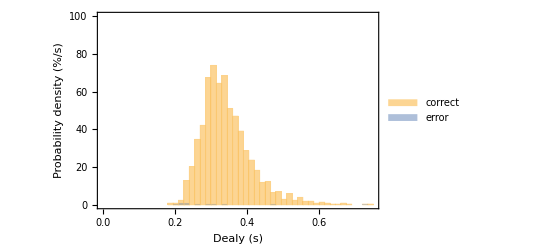

```mathematica
p1=Histogram[{Select[z,#>0.&],-Select[z,#<0.&]},{0.015},100 #2/Length@z/0.15&,PlotRange->{{0,0.75},{0,100}},Frame->True,FrameLabel->{"Dealy (s)","Probability density (%/s)"},LabelStyle->Directive[FontSize->14],FrameStyle->Directive[Thickness[0.0005]],ChartLegends->{"correct","error"}]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>"_rt_async_distractor.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

#### Cluster analysis per amplitude

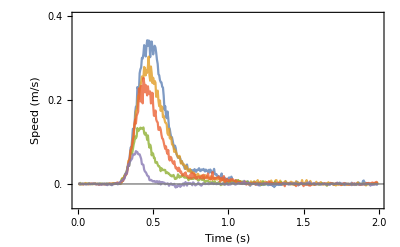

```mathematica
p1=PlotAlignRawEvents[Flatten[all[[plain]],1],2.,_?(#>1&)]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_speeds.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

#### effect of distractor

```mathematica
p1=Show[PlotMeanSpeedEvent[Flatten[all[[plain]],1],1.5,_?(#>100&)],PlotMeanSpeedEvent[Flatten[all[[distractor]],1],1.5,_?(#>100&)]];
```

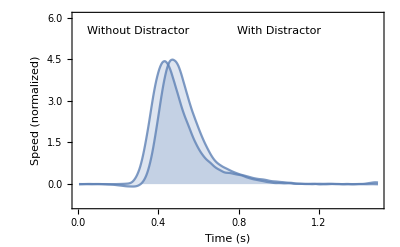

```mathematica
p1=Show[p1, Graphics[{Text["With Distractor",{1.0,5.5}],Text["Without Distractor",{0.3,5.5}]}]]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_distractor_effect.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

#### Effect of fatigue

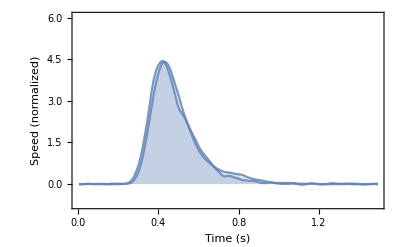

```mathematica
p1=Show[PlotMeanSpeedEvent[Flatten[Map[Take[#,4000]&,all[[plain]]],1],1.5,_?(#>100&)],PlotMeanSpeedEvent[Flatten[Map[Drop[#,4000]&,all[[plain]]],1],1.5,_?(#>100&)]]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_fatigue_effect.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

#### Summary of tests

```mathematica
p1=PlotMeanEvents[all[[plain]],1.5,_?(#>100&)];
```

```mathematica
p3=PlotMeanSpeedEvents[all[[plain]],1.5,_?(#>100&)];
```

```mathematica
p2=PlotMeanEvents[all[[distractor]],1.5,_?(#>100&)];
```

```mathematica
p4=PlotMeanSpeedEvents[all[[distractor]],1.5,_?(#>100&)];
```

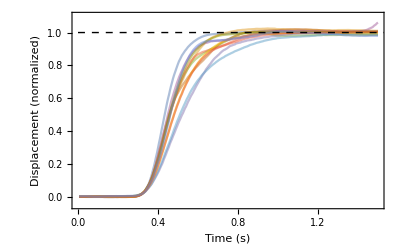
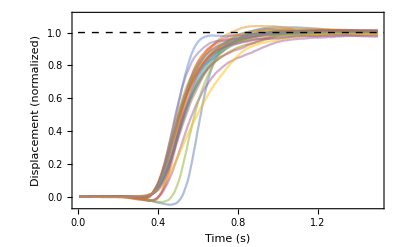
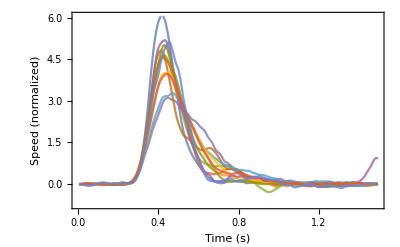
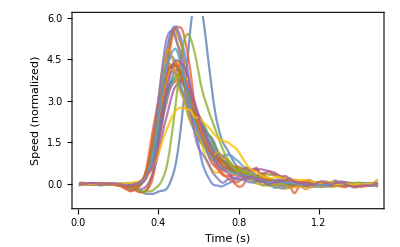
Katie  iPAD line test   17/11/14 - 01/12/14 | 
Without Distractor | With Distractor
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
pp=TableForm[{{"Without Distractor","With Distractor"},{p1,p2},{p3,p4}},TableHeadings->{None,{user<>"  iPAD line test"<>DateString[First@Sort@dates,{"   ","Day", "/","Month","/","YearShort"}]<>DateString[Last@Sort@dates,{" - ","Day", "/","Month","/","YearShort"}]}}]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_summary.tif",Rasterize[pp,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

#### Variations over time

```mathematica
plainweeks=DeleteCases[Map[Intersection[plain,#]&,weeks],_?(Length@#==0&)];
plainweekdates =Map[DateObject@Mean@Map[AbsoluteTime,dates[[#]]]&,plainweeks];
```

```mathematica
distractorweeks =DeleteCases[Map[Intersection[distractor,#]&,weeks],_?(Length@#==0&)];
distractorweekdates =Map[DateObject@Mean@Map[AbsoluteTime,dates[[#]]]&,distractorweeks];
```

```mathematica
RTplainweeks=Table[0.005Mean@ Abs@Flatten@Map[DelayCycles[#,2.,_?(#>100&)]&,all[[i]]],{i,plainweeks}];
RTdistractorweeks=Table[0.005Mean@ Abs@Flatten@Map[DelayCycles[#,2.,_?(#>100&)]&,all[[i]]],{i,distractorweeks}];
```

```mathematica
SDplainweeks=Table[0.005StandardDeviation@ Abs@Flatten@Map[DelayCycles[#,2.,_?(#>100&)]&,all[[i]]]/Length[Flatten@Map[DelayCycles[#,2.,_?(#>100&)]&,all[[i]]]]^0.5,{i,plainweeks}];
SDdistractorweeks=Table[0.005StandardDeviation@ Abs@Flatten@Map[DelayCycles[#,2.,_?(#>100&)]&,all[[i]]]/Length[Flatten@Map[DelayCycles[#,2.,_?(#>100&)]&,all[[i]]]]^0.5,{i,distractorweeks}];
```

```mathematica
ERTplainweeks=Table[100 Count[Flatten@Map[DelayCycles[#,2.,_?(#>100&)]&,all[[i]]],_?(#<0&)]/Length[Flatten@Map[DelayCycles[#,2.,_?(#>100&)]&,all[[i]]]],{i,plainweeks}];
ERTdistractorweeks=Table[100 Count[Flatten@Map[DelayCycles[#,2.,_?(#>100&)]&,all[[i]]],_?(#<0&)]/Length[Flatten@Map[DelayCycles[#,2.,_?(#>100&)]&,all[[i]]]],{i,distractorweeks}];
```

```mathematica
PSplainweeks =Table[Mean@Map[Max[200 Differences@Mean@AlignEvents[#,1.5,_?(#>100&)]]&,all[[i]]],{i,plainweeks}];
```

```mathematica
PSdistractorweeks =Table[Mean@Map[Max[200 Differences@Mean@AlignEvents[#,1.5,_?(#>100&)]]&,all[[i]]],{i,distractorweeks}];
```

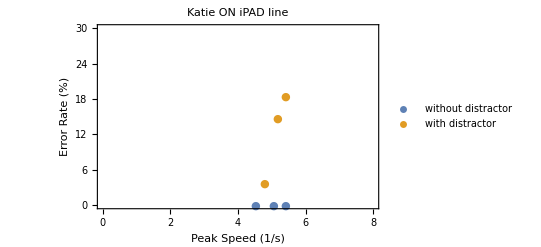

```mathematica
p1=ListPlot[{Transpose[{PSplainweeks,ERTplainweeks}],Transpose[{PSdistractorweeks,ERTdistractorweeks}]},Frame->True,PlotRange->{{0,8},{0,30}},FrameLabel->{{"Error Rate (%)",None},{"Peak Speed (1/s)",None}},PlotLabel->user<>" ON iPAD line",LabelStyle->{12,GrayLevel[0]},PlotLegends->Placed[{"without distractor","with distractor"},{0.25,0.825}],PlotMarkers->"●"]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_error_speed.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

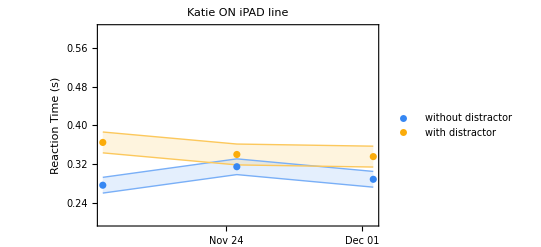

```mathematica
r=0;p1=DateListPlot[{Transpose[{plainweekdates,RTplainweeks}],Transpose[{distractorweekdates,RTdistractorweeks}],Transpose[{plainweekdates,GaussianFilter[RTplainweeks+2Mean@SDplainweeks,r]}],
Transpose[{plainweekdates,GaussianFilter[RTplainweeks-2Mean@ SDplainweeks,r]}],
Transpose[{distractorweekdates,GaussianFilter[RTdistractorweeks+2Mean@SDdistractorweeks,r]}],
Transpose[{distractorweekdates,GaussianFilter[RTdistractorweeks-2Mean@SDdistractorweeks,r]}]},
Joined->{False,False,True,True,True,True},PlotStyle->{ColorData[101,1],ColorData[101,2],{Thin,Lighter@ColorData[101,1]},{Thin,Lighter@ColorData[101,1]},{Thin,Lighter@ColorData[101,2]},{Thin,Lighter@ColorData[101,2]}},PlotRange->{0.2,0.6},FrameLabel->{{"Reaction Time (s)",None},{None,None}},PlotLabel->user<>" ON iPAD line",LabelStyle->{12,GrayLevel[0]},Filling->{3->{4},5->{6}},PlotLegends->Placed[{"without distractor","with distractor"},{0.775,0.825}]]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_rt_variation.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

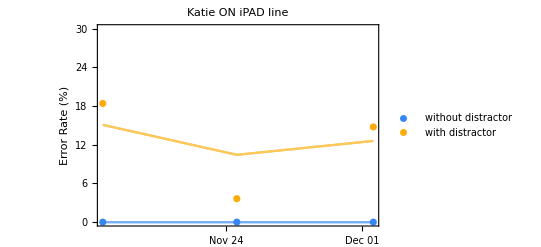

```mathematica
r=2;p1=DateListPlot[{Transpose[{plainweekdates,ERTplainweeks}],Transpose[{distractorweekdates,ERTdistractorweeks}],Transpose[{plainweekdates,GaussianFilter[ERTplainweeks,r]}],
Transpose[{plainweekdates,GaussianFilter[ERTplainweeks,r]}],
Transpose[{distractorweekdates,GaussianFilter[ERTdistractorweeks,r]}],
Transpose[{distractorweekdates,GaussianFilter[ERTdistractorweeks,r]}]},
Joined->{False,False,True,True,True,True},PlotStyle->{ColorData[101,1],ColorData[101,2],{Lighter@ColorData[101,1]},{Lighter@ColorData[101,1]},{Lighter@ColorData[101,2]},{Lighter@ColorData[101,2]}},PlotRange->{0,30},FrameLabel->{{"Error Rate (%)",None},{None,None}},PlotLabel->user<>" ON iPAD line",LabelStyle->{12,GrayLevel[0]},Filling->{3->{4},5->{6}},PlotLegends->Placed[{"without distractor","with distractor"},{0.775,0.825}]]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_errors_variation.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

#### Other reaction time charts

```mathematica
RT10M=Map[0.005 Mean[#]&,Quiet@Map[Delays[#,2.,_?(#>100&)]&,all]];
```

```mathematica
RTM=Map[0.005 Mean[Abs@#]&,Quiet@Map[DelayCycles[#,2.,_?(#>100&)]&,all]];
```

```mathematica
RT10SD=Map[0.005 StandardDeviation[#]&,Quiet@Map[Delays[#,2.,_?(#>100&)]&,all]];
```

```mathematica
PSmax =Map[Max[200 Differences@Mean@AlignEvents[#,1.5,_?(#>100&)]]&,all];
```

```mathematica
PSmin =Map[Min[200 Differences@Mean@AlignEvents[#,1.5,_?(#>100&)]]&,all];
```

```mathematica
morning=Flatten@Position[Map[DateValue[#,"Hour"]&,dates],_?(#<14&)];
```

```mathematica
afternoon=Flatten@Position[Map[DateValue[#,"Hour"]&,dates],_?(#>13&)];
```

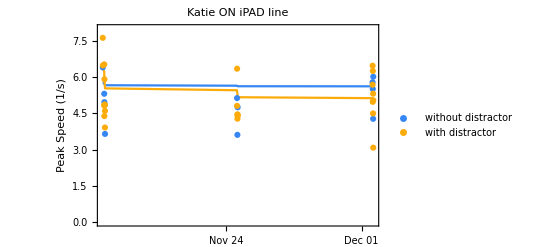

```mathematica
r=20;p1=DateListPlot[{Transpose[{dates,PSmax}][[plain]],Transpose[{dates,PSmax}][[distractor]],Transpose[{dates[[plain]],GaussianFilter[PSmax[[plain]],r]}],Transpose[{dates[[distractor]],GaussianFilter[PSmax[[distractor]],r]}]},Joined->{False,False,True,True},PlotStyle->{ColorData[101,1],ColorData[101,2],ColorData[101,1],ColorData[101,2]},PlotRange->{0,8},FrameLabel->{{"Peak Speed (1/s)",None},{None,None}},PlotLabel->user<>" ON iPAD line",LabelStyle->{12,GrayLevel[0]},PlotLegends->Placed[{"without distractor","with distractor"},{0.775,0.825}]]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_peaks_speed_variation.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

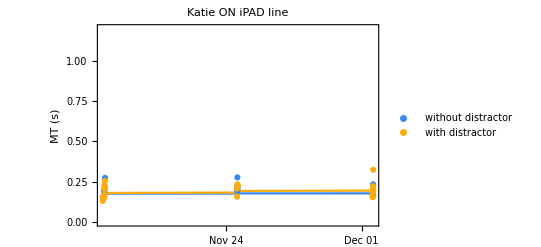

```mathematica
r=20;p1=Quiet@DateListPlot[{Transpose[{dates,1/PSmax}][[plain]],Transpose[{dates,1/PSmax}][[distractor]],Transpose[{dates[[plain]],1/GaussianFilter[PSmax[[plain]],r]}],Transpose[{dates[[distractor]],1/GaussianFilter[PSmax[[distractor]],r]}]},Joined->{False,False,True,True},PlotStyle->{ColorData[101,1],ColorData[101,2],ColorData[101,1],ColorData[101,2]},PlotRange->{0,1.2},FrameLabel->{{"MT (s)",None},{None,None}},PlotLabel->user<>" ON iPAD line",LabelStyle->{12,GrayLevel[0]},PlotLegends->Placed[{"without distractor","with distractor"},{0.775,0.825}]]
```

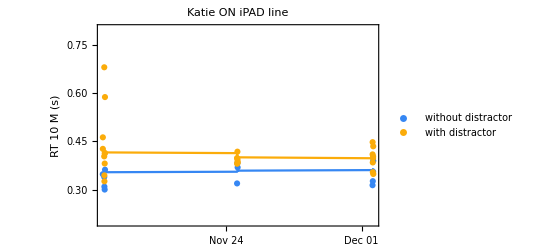

```mathematica
r=20;p1=DateListPlot[{Transpose[{dates,RT10M}][[plain]],Transpose[{dates,RT10M}][[distractor]],Transpose[{dates[[plain]],GaussianFilter[RT10M[[plain]],r]}],Transpose[{dates[[distractor]],GaussianFilter[RT10M[[distractor]],r]}]},Joined->{False,False,True,True},PlotStyle->{ColorData[101,1],ColorData[101,2],ColorData[101,1],ColorData[101,2]},PlotRange->{0.2,0.8},FrameLabel->{{"RT 10 M (s)",None},{None,None}},PlotLabel->user<>" ON iPAD line",LabelStyle->{12,GrayLevel[0]},PlotLegends->Placed[{"without distractor","with distractor"},{0.775,0.825}]]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_RT10M_variation.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

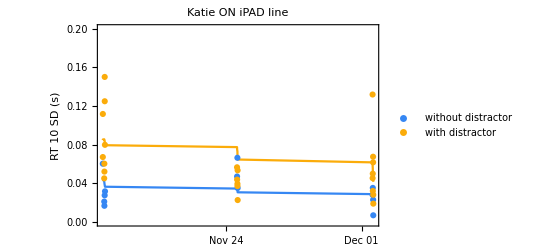

```mathematica
r=20;p1=DateListPlot[{Transpose[{dates,RT10SD}][[plain]],Transpose[{dates,RT10SD}][[distractor]],Transpose[{dates[[plain]],GaussianFilter[RT10SD[[plain]],r]}],Transpose[{dates[[distractor]],GaussianFilter[RT10SD[[distractor]],r]}]},Joined->{False,False,True,True},PlotStyle->{ColorData[101,1],ColorData[101,2],ColorData[101,1],ColorData[101,2]},PlotRange->{0.,0.2},FrameLabel->{{"RT 10 SD (s)",None},{None,None}},PlotLabel->user<>" ON iPAD line",LabelStyle->{12,GrayLevel[0]},PlotLegends->Placed[{"without distractor","with distractor"},{0.775,0.825}]]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_RT10SD_variation.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```

#### best/worst case

```mathematica
ibest=First@Flatten@Position[RT10M,Min[RT10M[[plain]]]]
```

10

```mathematica
iworst=First@Flatten@Position[RT10M,Max[RT10M[[plain]]]]
```

35

```mathematica
p8=Show[PlotMeanEvent[ImportTest[files[[ibest]]],2.,_?(#>100&)],PlotMeanEvent[ImportTest[files[[iworst]]],2.,_?(#>100&)]];
```

C:/Users/Line/notremor/build-FP_RehabPlatform-Desktop_Qt_5_3_MSVC2012_OpenGL_32bit-Debug/debug/User/Subject0002/line/20141117163429.txt

Minimum Sample Time (ms) 4

Mean Sample Time    (ms) 5.90134

Maximum Sample Time (ms) 21

Data is resampled at 5 ms, here is an excerpt

| Time (s) | Target | Disturbance | position/force
 | 0. | 960. | 0. | 957.
 | 0.005 | 960. | 0. | 958.25
 | 0.01 | 960. | 0. | 959.

N samples  5 0.953391

C:/Users/Line/notremor/build-FP_RehabPlatform-Desktop_Qt_5_3_MSVC2012_OpenGL_32bit-Debug/debug/User/Subject0002/line/20141201142950.txt

Minimum Sample Time (ms) 4

Mean Sample Time    (ms) 5.98807

Maximum Sample Time (ms) 15

Data is resampled at 5 ms, here is an excerpt

| Time (s) | Target | Disturbance | position/force
 | 0. | 960. | 0. | 959.
 | 0.005 | 960. | 0. | 961.
 | 0.01 | 960. | 0. | 964.

N samples  2 4.4645

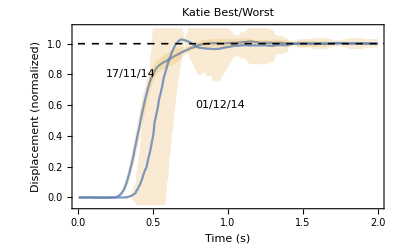

```mathematica
p1=Show[p8,Graphics[Text[DateString[dates[[ibest]],{"Day", "/","Month","/","YearShort"}],{0.35,0.8}]],Graphics[Text[DateString[dates[[iworst]],{"Day", "/","Month","/","YearShort"}],{0.95,0.6}]],PlotLabel->user<>" Best/Worst"]
```

```mathematica
Export[NotebookDirectory[]<>"/ Figures/"<>user<>"_best_worst.tif",Rasterize[p1,"Image",RasterSize->1500],"ImageEncoding"->"ZIP"];
```